```mathematica
Curve=ParametricPlot3D[{
{t,
(1/2)*t^2,
1}
},{t,0,3},PlotStyle->{Blue},AxesLabel->{x,y,z}];
P={2,2,1};

Tangent=ParametricPlot3D[{
{2+t,
2+2*t,
1+0}
},{t,-10,10},PlotStyle->{Green}];

Basepoint=Graphics3D[{RGBColor[1,0,1],{PointSize[0.025],Point[P]}}];

Legend=Graphics3D[{RGBColor[1,0,0],Text["P",P,{-1,2}]}];

Show[Curve,Tangent,Basepoint,Legend]
```

-Graphics3D-

```mathematica
Curve=ParametricPlot3D[{
{Cos[t],
Sin[t],
9*t}
},{t, 5.75, 7},PlotStyle->{Blue},AxesLabel->{x,y,z}];
P={1,0,18*Pi};

Tangent=ParametricPlot3D[{
{1+0,
0+t,
18*Pi+9*t}
},{t,-10,10},PlotStyle->{Green}];

Basepoint=Graphics3D[{RGBColor[1,0,1],{PointSize[0.025],Point[P]}}];

Legend=Graphics3D[{RGBColor[1,0,0],Text["P",P,{-1,2}]}];

Show[Curve,Tangent,Basepoint,Legend]
```

-Graphics3D-

```mathematica
Curve=ParametricPlot3D[{
{t,
t^2,
t^3}
},{t, 0, 1.5},PlotStyle->{Blue},AxesLabel->{x,y,z}];
P={1,1,1};

Tangent=ParametricPlot3D[{
{1+t,
1+t*2,
1+t*3}
},{t,-10,10},PlotStyle->{Green}];

Basepoint=Graphics3D[{RGBColor[1,0,1],{PointSize[0.025],Point[P]}}];

Legend=Graphics3D[{RGBColor[1,0,0],Text["P",P,{-1,2}]}];

Show[Curve,Tangent,Basepoint,Legend]
```

-Graphics3D-

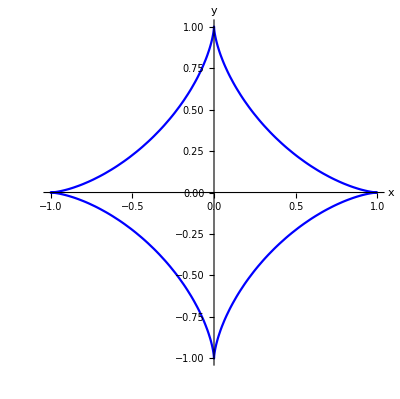

```mathematica
a=1;
Curve=ParametricPlot[{
{a*(Cos[t])^3,
a*(Sin[t])^3}
},{t, 0, 2*Pi},PlotStyle->{Blue},AxesLabel->{x,y}];

Show[Curve]
```

WolframAlphaQueryResults

(x==-1/3&&y==0&&z==0)||(-1/3<x<1/3&&-1/3 √(1-9 x^2)≤y≤1/3 √(1-9 x^2)&&(z==-√(1-9 x^2-9 y^2)||z==√(1-9 x^2-9 y^2)))||(x==1/3&&y==0&&z==0)

```mathematica
ContourPlot3D[9*(x^2+y^2)+z^2==1,
{x,-1,1},{y,-1,1},{z,-1,1},AxesLabel->{"x","y","z"}]
```

-Graphics3D-

WolframAlphaQueryResults

5 x^2+2 y^2==1

```mathematica
ContourPlot3D[5 x^2+2 y^2==1,
{x,-1,1},{y,-1,1},{z,-1,1},AxesLabel->{"x","y","z"}]
```

-Graphics3D-

```mathematica
39/3
```

13

WolframAlphaQueryResults

z==1+√(x^2+y^2)

```mathematica
ContourPlot3D[z-√(x^2+y^2)==0,
{x,-1,1},{y,-1,1},{z,0,1},AxesLabel->{"x","y","z"}]
```

-Graphics3D-